```mathematica
RHSexact[Le_,Lμ_,Lτ_]:=Block[{},
{le,lμ,lτ}={Le,Lμ,Lτ};
PoscEffναInserted[ms_,T_,p_,le,lμ,lτ]=PoscEffνα[10^-6 ms,p,le,lμ,lτ,gsint[T,le,lμ,lτ],μνeInt[T,le,lμ,lτ],μeInt[T,le,lμ,lτ],ΔnμInt[T,le,lμ,lτ],ΔnτInt[T,le,lμ,lτ],ΔLQstrongInt[T,le,lμ,lτ],T,GFval,mZval,mWval,sWval,Γαint[T,p,le,lμ,lτ]];
rhsIntegrandExactInserted[ms_,U2_,T_,p_,le,lμ,lτ]=dtdTint1[T,le,lμ,lτ]*U2*Γαint[T,p,le,lμ,lτ]/2*PoscEffναInserted[ms,T,p,le,lμ,lτ]*fναFDμ[p,T,μνeInt[T,le,lμ,lτ]]*(4Pi)/(2Pi)^3*p^2;
]
Do[
Module[{Le=f[[1]],Lμ=f[[2]],Lτ=f[[3]]},
RHSexact[Le,Lμ,Lτ]
]
,{f,datasetsKensukeAvailable}]
rhsIntegralExact[ms_,U2_,T_,Le_,Lμ_,Lτ_]:=NIntegrate[rhsIntegrandExactInserted[ms,U2,T,p,Le,Lμ,Lτ],{p,pmin[T,Le,Lμ,Lτ],pmax[T,Le,Lμ,Lτ]},Method->"InterpolationPointsSubdivision"]
rhsIntegralExactNearResonances[ms_,U2_,T_,Le_,Lμ_,Lτ_,δ_]:=Block[{},
{pminv,pmaxv}={pmin[T,Le,Lμ,Lτ],pmax[T,Le,Lμ,Lτ]};
{pres1v,pres2v}={presν1Inserted[ms,T,Le,Lμ,Lτ],presν2Inserted[ms,T,Le,Lμ,Lτ]};
piece1=If[pminv<pres1v<pmaxv,NIntegrate[rhsIntegrandExactInserted[ms,U2,T,p,Le,Lμ,Lτ],{p,pres1v-δ,pres1v+δ},Method->"InterpolationPointsSubdivision"],0.];
piece2=If[pminv<pres2v<pmaxv,NIntegrate[rhsIntegrandExactInserted[ms,U2,T,p,Le,Lμ,Lτ],{p,pres2v-δ,pres2v+δ},Method->"LocalAdaptive"],0.];
piece1+piece2
]
```

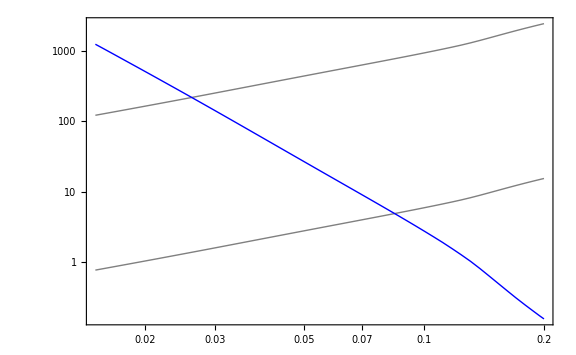

{2.6118×10^-50,0.00268656}

```mathematica
plotpminmax[ms_,let_,lμt_,lτt_]:=LogLogPlot[{10^3 pmin[T,let,lμt,lτt],10^3 pmax[T,let,lμt,lτt],10^3 presν2Inserted[ms,T,let,lμt,lτt]},{T,0.015,0.2},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large,PlotStyle->{{Thick,Gray},{Thick,Gray},{Thick,Blue}}]
{Letest,Lμtest,Lτtest}={0.035,-0.035,0.};
plotpminmax[5,Letest,Lμtest,Lτtest]
DynamicsnsρsInt[5.,10^-16.,Letest,Lμtest,Lτtest]
```

```mathematica
mstest=5.;
Tt=0.02;
U2v=10^-15.;
{let,lμt,lτt}={0.1,-0.1,0.};
Δpv[T_]=(pmax[T,let,lμt,lτt]-pmin[T,let,lμt,lτt])/200000. 10^3;
rhsIntegralExact[mstest,U2v,Tt,let,lμt,lτt]
{#,rhsIntegralExactNearResonances[mstest,U2v,Tt,let,lμt,lτt,#]}&/@(10^-#&/@{5,4,3,2})//N
dnsdt[mstest,U2v,Tt,le,lμ,lτ]
LogLogPlot[Δpv[T],{T,0.015,0.1}];
Table[{Tt,Δpv[Tt],100((dnsdt[mstest,U2v,Tt,le,lμ,lτ]-rhsIntegralExactNearResonances[mstest,U2v,Tt,let,lμt,lτt,Δpv[Tt]])/dnsdt[mstest,U2v,Tt,le,lμ,lτ])},{Tt,Table[t,{t,0.0155,0.05,0.001}]}]//TableForm
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.120978}. NIntegrate obtained -1.26578×10^-11 and 1.25582×10^-11 for the integral and error estimates.

-1.26578×10^-11

{{0.00001,-4.95549×10^-8},{0.0001,-4.95551×10^-8},{0.001,-4.95551×10^-8},{0.01,-4.95548×10^-8}}

-1.26432×10^-15

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

0.0155 | 0.000651009 | Indeterminate
0.0165 | 0.000695391 | Indeterminate
0.0175 | 0.000739668 | 100.
0.0185 | 0.00078394 | -6.77966×10^12
0.0195 | 0.000828196 | -3.49288×10^10
0.0205 | 0.00087249 | -5.84927×10^8
0.0215 | 0.000916785 | -2.31822×10^7
0.0225 | 0.000961131 | -1.76856×10^6
0.0235 | 0.00100565 | -216619.
0.0245 | 0.00105002 | -38235.8
0.0255 | 0.00109476 | -9077.42
0.0265 | 0.00113936 | -2678.17
0.0275 | 0.00118415 | -927.214
0.0285 | 0.00122924 | -341.781
0.0295 | 0.00127421 | -117.158
0.0305 | 0.00131947 | -18.9726
0.0315 | 0.0013647 | 23.4431
0.0325 | 0.00141013 | 48.8611
0.0335 | 0.0014558 | 63.3921
0.0345 | 0.00150143 | 72.2217
0.0355 | 0.00154718 | 77.8758
0.0365 | 0.00159306 | 81.6511
0.0375 | 0.00163901 | 84.2669
0.0385 | 0.00168515 | 86.1404
0.0395 | 0.00173133 | 87.5121
0.0405 | 0.0017776 | 88.546
0.0415 | 0.00182392 | 89.3373
0.0425 | 0.00187031 | 89.9516
0.0435 | 0.00191682 | 90.4413
0.0445 | 0.00196336 | 90.8317
0.0455 | 0.00200999 | 91.1468
0.0465 | 0.0020567 | 91.4064
0.0475 | 0.00210341 | 91.6191
0.0485 | 0.00215048 | 91.7994
0.0495 | 0.00219734 | 91.952

```mathematica
{pminv,pmaxv}
{pres1v,pres2v}
```

{0.00276395,0.442232}

{13493.,0.00709153}

rhsdep[0.000281519+x2]

rhsdep[x2]

InterpolatingFunction::dmval: Input value {0.024,0.00129284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

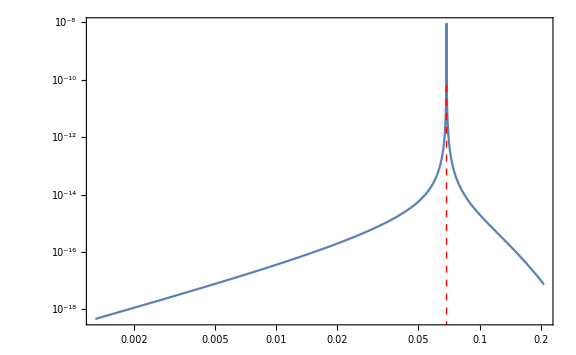

InterpolatingFunction::dmval: Input value {0.024,0.0686888} lies outside the range of data in the interpolating function. Extrapolation will be used.

835.3191}]]

```mathematica
plotres[ms_,U2_,T_,Le_,Lμ_,Lτ_]:=Module[{(*x1,x2*)},(*compute the two special p-values*)
x1=presν1Inserted[ms,T,Le,Lμ,Lτ];
x2=presν2Inserted[ms,T,Le,Lμ,Lτ];
rhsdep[p_]=-rhsIntegrandExactInserted[ms,U2,T,p,Le,Lμ,Lτ];
LogLogPlot[rhsdep[p],{p,pmin[T,Le,Lμ,Lτ],pmax[T,Le,Lμ,Lτ]},(*make sure we know the full vertical range*)PlotRange->All,(*draw two dashed red vertical lines at x1 and x2*)Epilog->{Dashed,Red,Thick,Line[{{Log[x1],Log[10^-30]},{Log[x1],Log[10^-10]}}],Line[{{Log[x2],Log[10^-30]},{Log[x2],Log[10^-10]}}]},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large]
]
Tv=0.024;
rhsdep[x2-RandomReal[{-Δpv[Tv]/2,Δpv[Tv]/2}]]
rhsdep[x2]
plotres[5,10^-15,0.024,0.1,-0.1,0.]
```

```mathematica
rhsdep[x2-RandomReal[{-Δpv[Tv]/2,Δpv[Tv]/2}]]
```

InterpolatingFunction::dmval: Input value {0.024,0.0682689} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.3895×10^-11

```mathematica
(*--------1. grid----------------------------------------------------*)
ClearAll[nBig,yMin,yMax,dy,yGrid,wTrap];
nBigg[T_]:=IntegerPart[T/0.015 2*10^5]
rhsIntegralGrid[ms_,U2_,T_,Le_,Lμ_,Lτ_]:=Module[{ys,ps,vals,ws},
{pminv,pmaxv}={pmin[T,Le,Lμ,Lτ],pmax[T,Le,Lμ,Lτ]};
{x1,x2}={presν1Inserted[ms,T,Le,Lμ,Lτ],presν2Inserted[ms,T,Le,Lμ,Lτ]};
Δp=(pmaxv-pminv)/(nBigg[T]-1);
pvals=(pminv+#*Δp)&/@Range[0,nBigg[T]-1];
vals=rhsIntegrandExactInserted[ms,U2,T,#,Le,Lμ,Lτ]&/@pvals;
Total[vals]*Δp
];
```

0.00279334

0.446935

(2.14821×10^-16 InterpolatingFunction[…][0.024,p_])/((1+ⅇ^(-1.91447+41.6667 p_)) ((1.81981×10^-10-1/(80000000000 p_)-6.62182×10^-15 p_)^2+1/4 (InterpolatingFunction[…][0.024,p_])^2))

```mathematica
Tv=0.019;
rhsIntegralGrid[5,10^-15,Tv,0.1,-0.1,0.]
rhsIntegralExactNearResonances[5,10^-15,Tv,0.1,-0.1,0.,0.003]
{x2,x1}
{pminv,pmaxv}
```

InterpolatingFunction::dmval: Input value {0.019,0.00101394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.019,0.00101457} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-1.39479×10^-9

-2.02878×10^-8

{0.141992,33920.4}

{0.00101394,0.16223}

```mathematica
Δp
```

8.94619×10^-7

```mathematica
Lτ//Clear
```

```mathematica
{pmin[T,Le,Lμ,Lτ],pmax[T,Le,Lμ,Lτ]}/.{T->0.02,Le->0.1,Lμ->-0.1,Lτ->0.}
```

{0.0010696,0.171136}

```mathematica
ClearAll[nBig,yMin,yMax,dy,yGrid,wTrap];
nBig=2*10^5;                     (*same resolution as python*)
yMin=0.1;yMax=16.;
dy=(yMax-yMin)/(nBig-1);

yGrid=Table[yMin+dy (i-1),{i,nBig}];
wTrap=ConstantArray[dy,nBig];wTrap[[{1,-1}]]*=1/2;

(*---------------------------------------------------------------*)
(*1. entropy-ratio helper:aFsol.b3 s(T)=s_ini⇒aFsol=(s_ini/s).b9ᐟ.b3*)
(*(You already have aFsol[T,Le,Lμ,Lτ] in memory)*)
(*---------------------------------------------------------------*)

(*---------------------------------------------------------------*)
(*2. grid integrator that uses your existing integrand*)
(*---------------------------------------------------------------*)
ClearAll[rhsIntegralGridFixed]

rhsIntegralGridFixed[ms_,U2_,T_,Le_,Lμ_,Lτ_]:=Module[{aF,pVals,vals,weights},aF=aFsol[T,Le,Lμ,Lτ];(*aFsol=(s_ini/s).b9ᐟ.b3*)
pVals=yGrid/aF;(*p=y/aFsol*)vals=rhsIntegrandExactInserted[ms,U2,T,#,Le,Lμ,Lτ]&/@pVals;
weights=wTrap/aF;(*dp=dy/aFsol*)Total[weights*vals]                    (*prefactor already*)]                                        (*inside integrand*)
```

InterpolatingFunction::dmval: Input value {0.02,0.000107445} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02,0.000107531} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-4.25119×10^-19

```mathematica
Tbench=0.025;                  (*25 MeV*)
msBench=5;
U2Bench=10^-15;
{LeBench,LμBench,LτBench}={0.10,-0.10,0.};

rhsGrid=rhsIntegralGridFixed[msBench,U2Bench,Tbench,LeBench,LμBench,LτBench];

δ=10^-4;                 (*narrow window around p_res*)
rhsRef=rhsIntegralExactNearResonances[msBench,U2Bench,Tbench,LeBench,LμBench,LτBench,δ];

Print["ratio grid / reference = ",NumberForm[rhsGrid/rhsRef,{4,3}]]
```

InterpolatingFunction::dmval: Input value {0.025,0.000135547} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.025,0.000135654} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ratio grid / reference = 1.354×10^-11